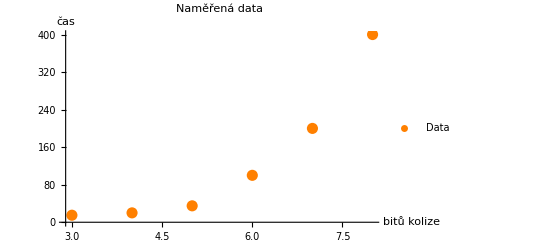

{a→1.28618,b→1.03584}

Model doby hledání x bitů kolize: 1.28618 2^(1.03584 x)

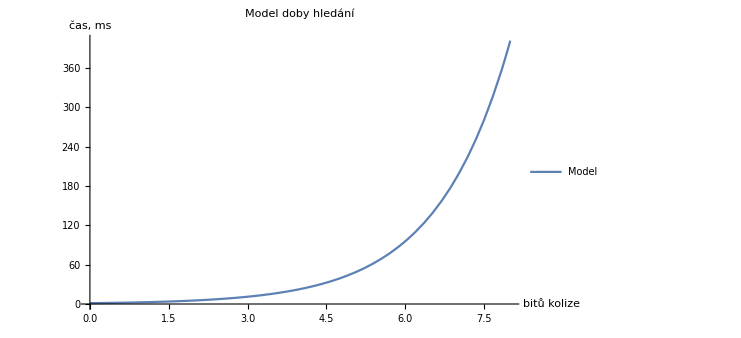

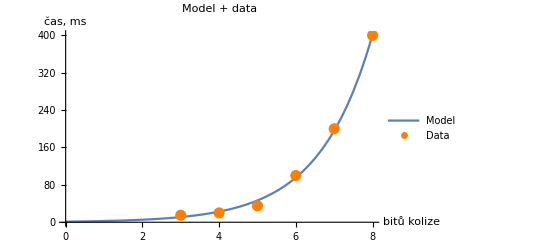

512 bitů kolize se bude hledat: 5.77079×10^159

```mathematica
(*data ve formátu:{{počet bitů kolize,doba hledání},{.,.},...}*)data={{3,15},{4,20},{5,35},{6,100},{7,200},{8,400}};
varListPlot=ListPlot[data,PlotLabel->"Naměřená data",AxesLabel->{"bitů kolize","čas"},PlotStyle->{Orange,PointSize[0.02]},PlotLegends->{"Data"}]

(*funkce,která nám bude modelovat dobu hledání*)
function:=a*2^(b*x)

(*nalezení parametrů a,b*)
foundVars=FindFit[data,function,{a,b},{x}]

(*dosazení parametrů do funkce*)
foundFunction:=function/. foundVars
Print["Model doby hledání x bitů kolize: ",foundFunction]

(*vykreslíme model*)
plotFunction=Plot[foundFunction,{x,0,8},PlotLabel->"Model doby hledání",AxesLabel->{"bitů kolize","čas, ms"},PlotLegends->{"Model"}]

(*vykreslíme model a přes ně naměřená data (zda model sedí)*)
Show[plotFunction,varListPlot,PlotLabel->"Model + data"]

(*Doba hledání plné kolize:do funkce dosadíme x=512*)
Print["512 bitů kolize se bude hledat: ",foundFunction/. x->512]
```